```mathematica
g0=√ϵ0 Cos[ϕ0];
g1=√ϵ1 √(1-ϵ0/ϵ1 Sin[ϕ0]^2);
g2=√ϵ2 √(1-ϵ0/ϵ2 Sin[ϕ0]^2);
α0=(√ϵ0)/Cos[ϕ0];
α1=(√ϵ1)/(√(1-ϵ0/ϵ1 Sin[ϕ0]^2));
α2=(√ϵ2)/(√(1-ϵ0/ϵ2 Sin[ϕ0]^2));
r01p=(α1-α0)/(α1+α0);
r12p=(α2-α1)/(α1+α2);
r01s=(g0-g1)/(g0+g1);
r12s=(g1-g2)/(g1+g2);
```

```mathematica
δ:=ω/c d √(ϵ1-ϵ0 Sin[ϕ0]^2);
Rp:=(r01p+r12p Exp[-2 I δ])/(1+r01p r12p Exp[-2 I δ])Exp[-2 I *(-ω/c √ϵ0 Cos[ϕ0]) d];
Rs:=(r01s+r12s Exp[-2 I δ])/(1+r01s r12s Exp[-2 I δ])Exp[-2 I *(-ω/c √ϵ0 Cos[ϕ0]) d];
```

```mathematica
ϵ0=1;
ϵ2=2.05;
c=3*10^8;
ω=2*Pi*32*10^9;
d=70*10^-6;
ϕ0=Pi/3;
```

```mathematica
ϵ1=1-(1/(215*70*10^-6))/(8.85*10^-12*ω)I;
```

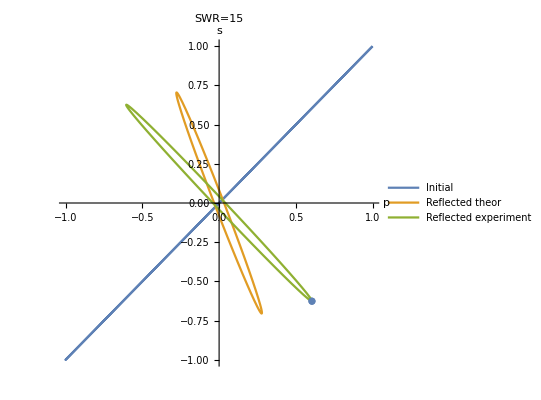

```mathematica
Show[ParametricPlot[{Re[{Exp[I ω t],Exp[I ω t]}],Re[{Exp[I ω t]*Rp,Exp[I ω t]*Rs}],{10^((-10.5+9.3)/20)Cos[ω t]*Cos[-46/360*2Pi]-10^((-40+9.3)/20)Sin[ω t]*Sin[-46/360*2Pi],10^((-10.5+9.3)/20)Cos[ω t]*Sin[-46/360*2Pi]+10^((-40+9.3)/20)Sin[ω t]*Cos[-46/360*2Pi]}},{t,0,2Pi/ω},AxesLabel->{"p","s"},PlotLegends->{"Initial","Reflected theor","Reflected experiment"},PlotLabel->"SWR=15"],ListPolarPlot[{{-46/360*2Pi,10^((-10.5+9.3)/20)}}]]
```

```mathematica
ϵ1=1-(1/(327*70*10^-6))/(8.85*10^-12*ω)I;
```

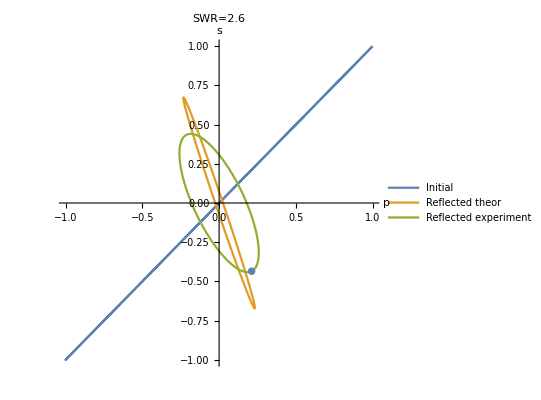

```mathematica
Show[ParametricPlot[{Re[{Exp[I ω t],Exp[I ω t]}],Re[{Exp[I ω t]*Rp,Exp[I ω t]*Rs}],{10^((-15.6+9.3)/20)Cos[ω t]*Cos[-64/360*2Pi]-10^((-25+9.3)/20)Sin[ω t]*Sin[-64/360*2Pi],10^((-15.6+9.3)/20)Cos[ω t]*Sin[-64/360*2Pi]+10^((-25+9.3)/20)Sin[ω t]*Cos[-64/360*2Pi]}},{t,0,2Pi/ω},AxesLabel->{"p","s"},PlotLegends->{"Initial","Reflected theor","Reflected experiment"},PlotLabel->"SWR=2.6"],ListPolarPlot[{{-64/360*2Pi,10^((-15.6+9.3)/20)}}]]
```

```mathematica
ϵ1=1-(1/(215*70*10^-6))/(8.85*10^-12*ω)I;
```

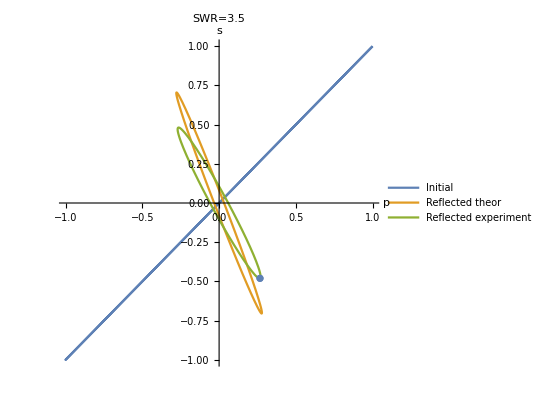

```mathematica
Show[ParametricPlot[{Re[{Exp[I ω t],Exp[I ω t]}],Re[{Exp[I ω t]*Rp,Exp[I ω t]*Rs}],{10^((-14.5+9.3)/20)Cos[ω t]*Cos[-61/360*2Pi]-10^((-35+9.3)/20)Sin[ω t]*Sin[-61/360*2Pi],10^((-14.5+9.3)/20)Cos[ω t]*Sin[-61/360*2Pi]+10^((-35+9.3)/20)Sin[ω t]*Cos[-61/360*2Pi]}},{t,0,2Pi/ω},AxesLabel->{"p","s"},PlotLegends->{"Initial","Reflected theor","Reflected experiment"},PlotLabel->"SWR=3.5"],ListPolarPlot[{{-61/360*2Pi,10^((-14.5+9.3)/20)}}]]
```